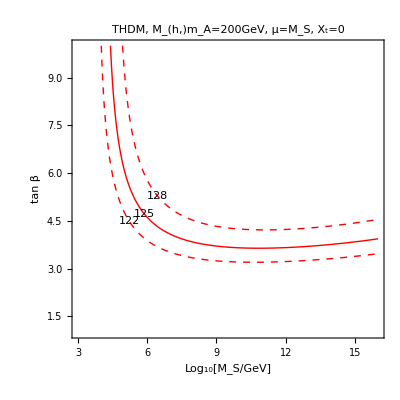

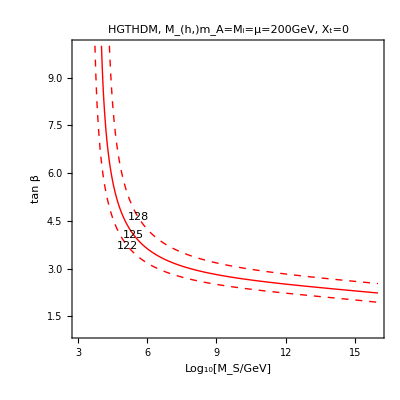

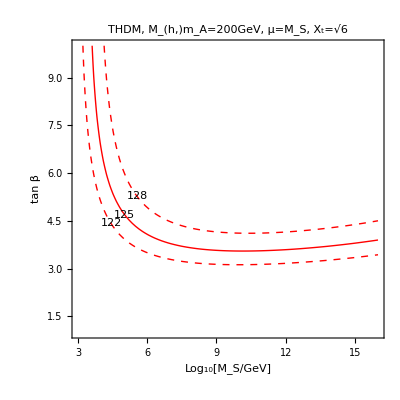

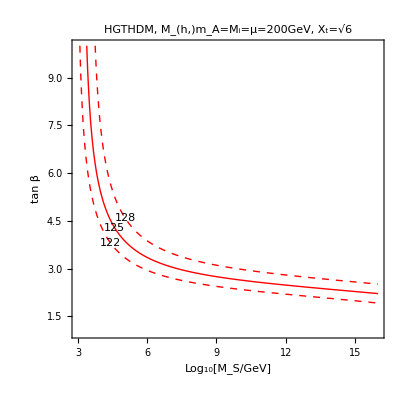

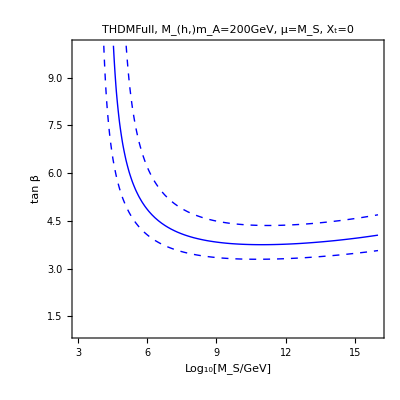

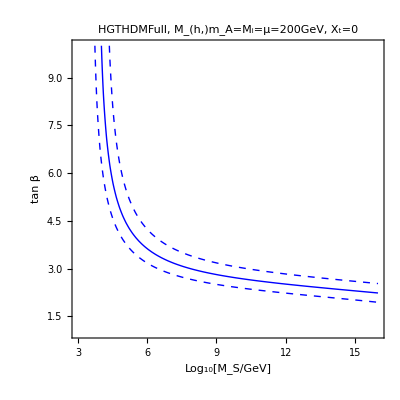

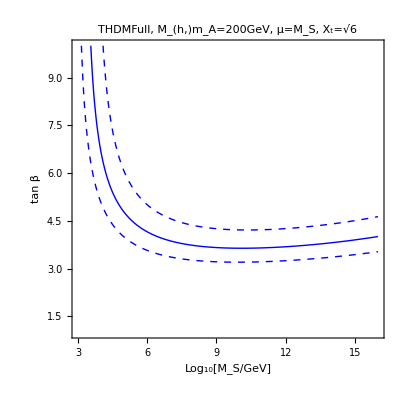

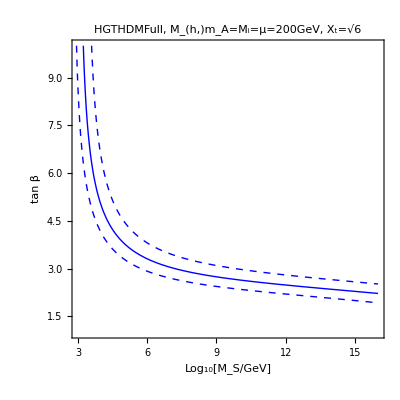

```mathematica
models={
{"THDMIIMSSMBC", "THDMIIMSSMBC_Xt-0.dat",0,Indeterminate,"THDM, M_(h,)m_A=200GeV, μ=M_S, X_t=0"},
{"HGTHDMIIMSSMBC", "HGTHDMIIMSSMBC_Xt-0.dat",0,Indeterminate,"HGTHDM, M_(h,)m_A=M_i=μ=200GeV, X_t=0"},
{"THDMIIMSSMBC", "THDMIIMSSMBC_Xt-2.44949.dat",√6,Indeterminate,"THDM, M_(h,)m_A=200GeV, μ=M_S, X_t=√6"},
{"HGTHDMIIMSSMBC", "HGTHDMIIMSSMBC_Xt-2.44949.dat",√6,Indeterminate,"HGTHDM, M_(h,)m_A=M_i=μ=200GeV, X_t=√6"},
{"THDMIIMSSMBCFull", "THDMIIMSSMBCFull_Xt-0.dat",0,Indeterminate,"THDMFull, M_(h,)m_A=200GeV, μ=M_S, X_t=0"},
{"HGTHDMIIMSSMBCFull", "HGTHDMIIMSSMBCFull_Xt-0.dat",0,Indeterminate,"HGTHDMFull, M_(h,)m_A=M_i=μ=200GeV, X_t=0"},
{"THDMIIMSSMBCFull", "THDMIIMSSMBCFull_Xt-2.44949.dat",√6,Indeterminate,"THDMFull, M_(h,)m_A=200GeV, μ=M_S, X_t=√6"},
{"HGTHDMIIMSSMBCFull", "HGTHDMIIMSSMBCFull_Xt-2.44949.dat",√6,Indeterminate,"HGTHDMFull, M_(h,)m_A=M_i=μ=200GeV, X_t=√6"}
};

For[i=1, i≤Length[models],i++,
fileName=models[[i,2]];
data=Select[
ImportString[
StringReplace[
Import[fileName,"Text"],
{StartOfLine~~"#"~~Shortest[___]~~EndOfLine~~"\n"->"",StartOfLine~~Except["\n"]..~~"-"~~EndOfLine~~"\n"->""}
],"Table"],
(#=!={})&
];
logData={Log[10,#[[2]]],#[[1]],#[[3]]}&/@data;
pmStyle=If[i≤4,Directive[Red,Dashed],Directive[Blue,Dashed]];
MhStyle=If[i≤4,Directive[Red,Thick],Directive[Blue,Thick]];
models[[i,4]]=
ListContourPlot[logData,
PlotLegends->Automatic,
PlotLabel->models[[i,5]],
PlotRange->{{Log[10,10^3],Log[10,10^16]},{1,10}},
FrameLabel->{"Log_10[M_S/GeV]","tan β"},
Contours->{122,125,128},
ContourShading->None,
ContourLabels->If[i≤4,All,None],
ContourStyle->{pmStyle,MhStyle,pmStyle}
];
Print[models[[i,4]]];
Export[models[[i,1]]<>"_Xt-"<>ToString[models[[i,3]]]<>".pdf",models[[i,4]]];
];
```

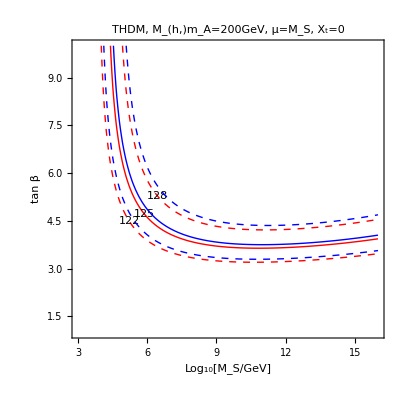

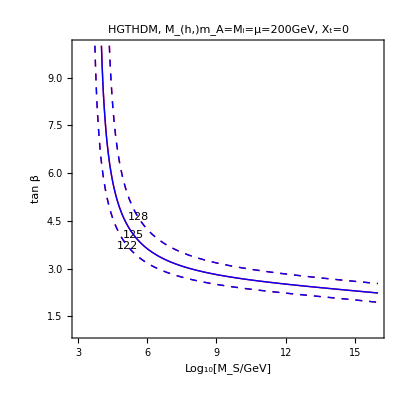

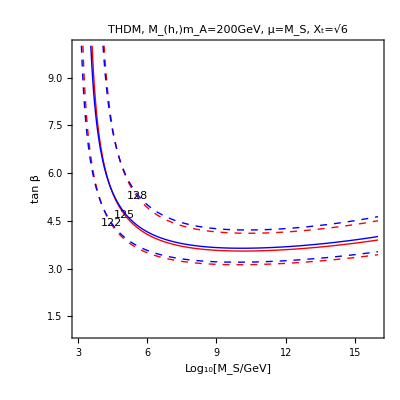

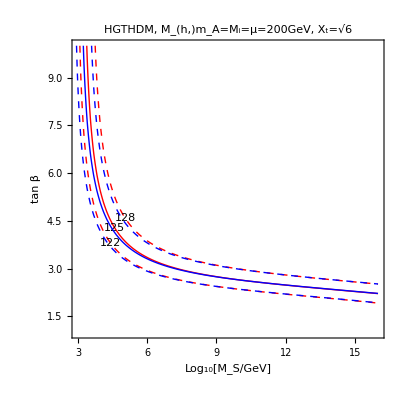

```mathematica
combined=Table[0,{i,1,Length[models]/2}];

For[i=1,i≤Length[models]/2,i++,
combined[[i]]=Show[models[[i,4]],models[[i+4,4]]];
Print[combined[[i]]];
Export[models[[i,1]]<>"_Xt-"<>ToString[models[[i,3]]]<>"_combined.pdf",combined[[i]]];
];
```